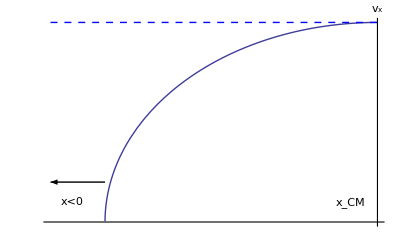

```mathematica
Show[Plot[Sqrt[1-x^2],{x,-1.2,0},PlotStyle->Directive[Thick]],Graphics[Text[Style["x_CM",Large],{-0.1,0.1}]], Graphics[Arrow[{{-1,0.2},{-1.2,0.2}}]],Graphics[Text[Style[x<0,Large],{-1.12,0.1}]],Graphics[{Thick,Dashed,Blue,Line[{{-1.2,1},{0,1}}]}],AxesStyle->Directive[Thick],Ticks->None,AxesLabel->{None,Style["v_x",Large]}]
```

```mathematica
Export["sat.eps",%103,"EPS"]
```

sat.eps

```mathematica
a=Import["~/Documents/trattatello/trenino.jpg"]
```

-Graphics-

```mathematica
a
```

-Graphics-

```mathematica
b=Image[a,"Bit16"]
```

-Graphics-